# QEA - Attitude Control - B-set 2

```mathematica
SetDirectory@NotebookDirectory[];
<<"../General.m"
```

```mathematica
b=2
```

2

```mathematica
b'
```

0&

```mathematica
b:=b
```

```mathematica
b'
```

b'

```mathematica
Solve[m Derivative[Derivative[x]]==-T Cos[θ]&&m Derivative[Derivative[y]]==T Sin[θ]-m g&&x Derivative[Derivative[x]]+y Derivative[Derivative[y]]==-Derivative[x]-Derivative[y],{Derivative[Derivative[x]],Derivative[Derivative[y]],T}]
```

{{Derivative[Derivative[x]]→-(g y Cos[θ]-Cos[θ] Derivative[x]-Cos[θ] Derivative[y])/(-x Cos[θ]+y Sin[θ]),Derivative[Derivative[y]]→-(-g x Cos[θ]+Derivative[x] Sin[θ]+Derivative[y] Sin[θ])/(-x Cos[θ]+y Sin[θ]),T→-(m (g y-Derivative[x]-Derivative[y]))/(x Cos[θ]-y Sin[θ])}}

## Basic Pendulum

```mathematica
With[{context="basicpendulum`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{m=1,g=9.8,l=1},initialConditions={θ[0]==π/2,θ'[0]==0};
de={θ''[t]==-m g Sin[θ[t]]/l};
sol=NDSolveValue[Join[initialConditions,de],θ[t],{t,0,10}]
]
```

InterpolatingFunction[{{0., 10.}}, <>][t]

### Animation of pendulum

```mathematica
Animate[ParametricPlot[{Sin[sol],-Cos[sol]},{t,n,n+.1},PlotRange->{{-1,1},{-1,1}}],{n,0,9.9}]
```

### Plot of the path the pendulum covers starting with initial conditions θ[0]=π/2 and θ’[0]=0

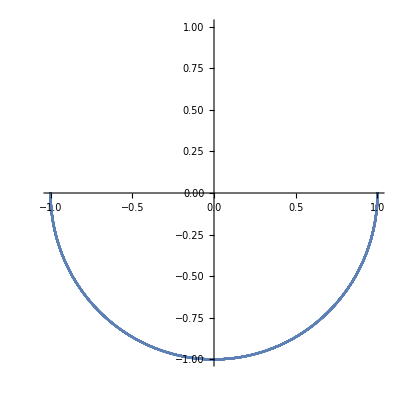

```mathematica
ParametricPlot[{Sin[sol],-Cos[sol]},{t,0,10},PlotRange->{{-1,1},{-1,1}}]
```

### Plot of θ over time with initial conditions θ[0]=π/2 and θ’[0]=0

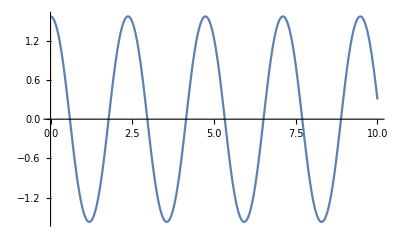

```mathematica
Plot[sol,{t,0,10}]
```

### Now let’s calculate angular velocity → kinetic energy

```mathematica
With[{m=1,g=9.8,l=1},initialConditions={θ[0]==π/2,θ'[0]==0};
de={θ''[t]==-m g Sin[θ[t]]/l};
sol2=NDSolveValue[Join[initialConditions,de],θ'[t],{t,0,10}]
]
```

InterpolatingFunction[{{0., 10.}}, <>][t]

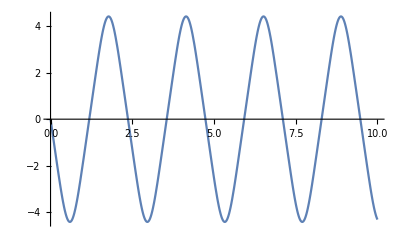

```mathematica
Plot[sol2,{t,0,10}]
```

### Calculate the inertia of the point mass

```mathematica
With[{m=1,g=9.8,l=1},
inertia=m l^2;
rKinetic=1/2 inertia sol2^2;
]
```

### Plot rotational kinetic energy over time

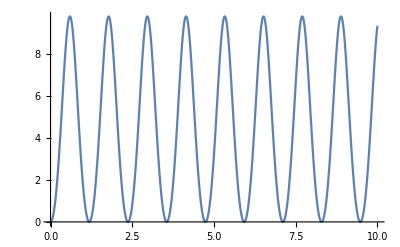

```mathematica
Plot[rKinetic,{t,0,10}]
```

### Calculate potential energy

```mathematica
With[{m=1,g=9.8,l=1},
potential=m g (-Cos[sol])]
```

-9.8 Cos[InterpolatingFunction[{{0., 10.}}, <>][t]]

### Plot of potential energy (blue), kinetic energy (yellow), and total energy (green)

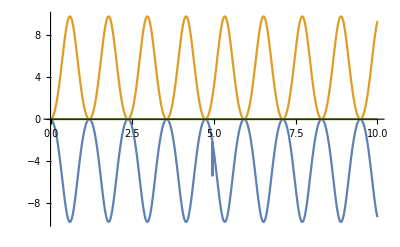

```mathematica
Plot[{potential,rKinetic,potential+rKinetic},{t,0,10}]
```

```mathematica
With[{context="basicpendulum`"},If[Context[]==context,End[],"Not in context"]]
```

basicpendulum`

```mathematica
With[{context="damping`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

### damping just based on v

```mathematica
With[{m=1,g=9.8,l=1},initialConditions={θ[0]==π/2,θ'[0]==0};
de={θ''[t]==-m g Sin[θ[t]]/l-θ'[t]};
sol=NDSolveValue[Join[initialConditions,de],θ[t],{t,0,10}]
]
```

InterpolatingFunction[{{0., 10.}}, <>][t]

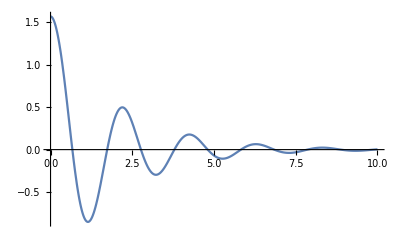

```mathematica
Plot[sol,{t,0,10},PlotRange->Full]
```

```mathematica
Animate[ParametricPlot[{Sin[sol],-Cos[sol]},{t,n,n+.1},PlotRange->{{-1,1},{-1,1}}],{n,0,9.9}]
```

```mathematica
With[{context="damping`"},If[Context[]==context,End[],"Not in context"]]
```

damping`

### v^2 damping like air resistance

```mathematica
With[{m=1,g=9.8,l=1},initialConditions={θ[0]==π/2,θ'[0]==0};
de={θ''[t]==-m g Sin[θ[t]]/l-Abs[θ'[t]]θ'[t]};
sol=NDSolveValue[Join[initialConditions,de],θ[t],{t,0,10}]
]
```

InterpolatingFunction[{{0., 10.}}, <>][t]

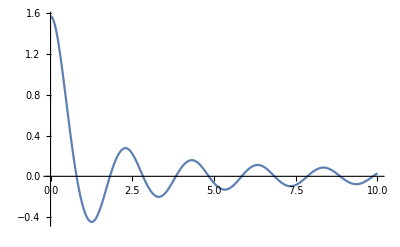

```mathematica
Plot[sol,{t,0,10},PlotRange->Full]
```

```mathematica
Animate[ParametricPlot[{Sin[sol],-Cos[sol]},{t,n,n+.1},PlotRange->{{-1,1},{-1,1}}],{n,0,9.9}]
```

```mathematica
With[{context="damping`"},If[Context[]==context,End[],"Not in context"]]
```

Not in context

## Springy

```mathematica
With[{context="springy`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

### Solve differential equations with specified initial conditions

```mathematica
With[{m=1,g=9.8,l0=1,k=2},initialConditions={θ[0]==π/2,θ'[0]==0,l[0]==1,l'[0]==0};
de={θ''[t]== (-m g Sin[θ[t]]-2l'[t] θ'[t])/l[t],l''[t]==-k/m(l[t]-l0)+g Cos[θ[t]]+l[t] θ'[t]^2};
{θSol,lSol}=NDSolveValue[Join[initialConditions,de],{θ[t],l[t]},{t,0,30}]
]
```

{InterpolatingFunction[{{0., 30.}}, <>][t],InterpolatingFunction[{{0., 30.}}, <>][t]}

### Plot of the angle over time. Those bars at the end look really strange. θ'[t]^2 must have broken it again.

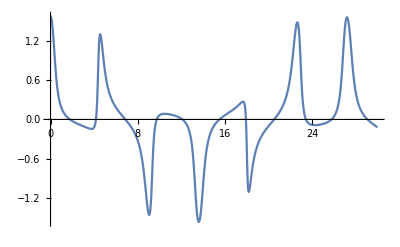

```mathematica
Plot[θSol,{t,0,30},PlotRange->Full]
```

### Plot of the length over time

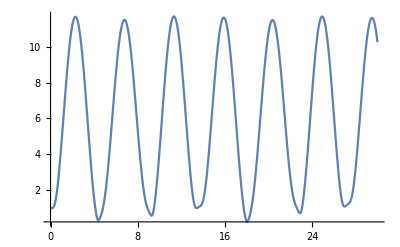

```mathematica
Plot[lSol,{t,0,30},PlotRange->Full]
```

### Animation of springy pendulum

```mathematica
Animate[ParametricPlot[{lSol Sin[θSol],-lSol Cos[θSol]},{t,n,n+.1},PlotRange->{{-15,15},{-15,15}}],{n,0,29.9}]
```

```mathematica
With[{context="springy`"},If[Context[]==context,End[],"Not in context"]]
```

springy`